```mathematica
ALPHA = 3.3;
h = 0.4;
PHI[x_,y_]:=(ALPHA^2+1)*x+(1-ALPHA)*y
PSI[x_,y_]:=(1- ALPHA)*x^2+ALPHA*y^2+2*ALPHA
GAMMA[x_,y_]:=Sqrt[4-y^2]-Abs[x] ;
```

```mathematica
xn=# h&/@Range[-5,5];
yn = # h&/@Range[-5,5];
xn
yn
```

{-2.,-1.6,-1.2,-0.8,-0.4,0.,0.4,0.8,1.2,1.6,2.}

{-2.,-1.6,-1.2,-0.8,-0.4,0.,0.4,0.8,1.2,1.6,2.}

```mathematica
Flatten[Outer[{#1, #2}&, xn, yn], 1];
set=Select[%, (#⟦1⟧)^2+(#⟦2⟧)^2<=4&];
```

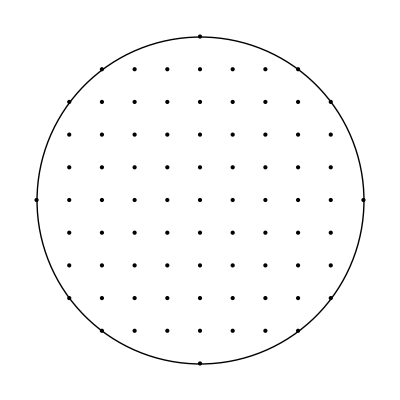

```mathematica
Graphics[{Point/@set, Circle[{0,0},2]}]
```

```mathematica
variables = Subscript[f, Round[#[[1]]/h], Round[#[[2]]/h]]&/@set;
```

```mathematica
conditions={
Subscript[f, 0, 5]==PSI[xn[[6]],yn[[11]] ],
Subscript[f, 5, 0]==PSI[xn[[11]],yn[[6]] ],
Subscript[f, 0, -5]==PSI[xn[[6]],yn[[1]] ],
Subscript[f, -5, 0]==PSI[xn[[1]],yn[[6]] ],
Subscript[f, 1, 4]==(h*PSI[xn[[7]],yn[[10]]+GAMMA[xn[[7]],yn[[10]]]]+GAMMA[xn[[7]],yn[[10]]] Subscript[f, 1,3])/(h+GAMMA[xn[[7]],yn[[10]]]),
Subscript[f, 2, 4]==(h*PSI[xn[[8]],yn[[10]]+GAMMA[xn[[8]],yn[[10]]]]+GAMMA[xn[[8]],yn[[10]]] Subscript[f, 2,3])/(h+GAMMA[xn[[7]],yn[[10]]]),
Subscript[f, 4, 1]==(h*PSI[xn[[10]],yn[[7]]+GAMMA[xn[[10]],yn[[7]]]]+GAMMA[xn[[10]],yn[[7]]] Subscript[f, 3,1])/(h+GAMMA[xn[[10]],yn[[7]]]),
Subscript[f, 4, 2]==(h*PSI[xn[[10]],yn[[8]]+GAMMA[xn[[10]],yn[[8]]]]+GAMMA[xn[[10]],yn[[8]]] Subscript[f, 3,2])/(h+GAMMA[xn[[10]],yn[[8]]]),

Subscript[f, -1, 4]==(h*PSI[xn[[5]],yn[[10]]+GAMMA[xn[[5]],yn[[10]]]]+GAMMA[xn[[5]],yn[[10]]] Subscript[f, -1,3])/(h+GAMMA[xn[[5]],yn[[10]]]),
Subscript[f, -2, 4]==(h*PSI[xn[[4]],yn[[10]]+GAMMA[xn[[4]],yn[[10]]]]+GAMMA[xn[[4]],yn[[10]]] Subscript[f, -2,3])/(h+GAMMA[xn[[4]],yn[[10]]]),
Subscript[f, -4, 1]==(h*PSI[xn[[2]],yn[[7]]+GAMMA[xn[[2]],yn[[7]]]]+GAMMA[xn[[2]],yn[[7]]] Subscript[f, -3,1])/(h+GAMMA[xn[[2]],yn[[7]]]),
Subscript[f, -4, 2]==(h*PSI[xn[[2]],yn[[8]]+GAMMA[xn[[2]],yn[[8]]]]+GAMMA[xn[[2]],yn[[8]]] Subscript[f, -3,2])/(h+GAMMA[xn[[2]],yn[[8]]]),

Subscript[f, 1, -4]==(h*PSI[xn[[7]],yn[[2]]+GAMMA[xn[[7]],yn[[2]]]]+GAMMA[xn[[7]],yn[[2]]] Subscript[f, 1,-3])/(h+GAMMA[xn[[7]],yn[[2]]]),
Subscript[f, 2, -4]==(h*PSI[xn[[8]],yn[[2]]+GAMMA[xn[[8]],yn[[2]]]]+GAMMA[xn[[8]],yn[[2]]] Subscript[f, 2,-3])/(h+GAMMA[xn[[8]],yn[[2]]]),
Subscript[f, 4, -1]==(h*PSI[xn[[10]],yn[[5]]+GAMMA[xn[[10]],yn[[5]]]]+GAMMA[xn[[10]],yn[[5]]] Subscript[f, 3,-1])/(h+GAMMA[xn[[10]],yn[[5]]]),
Subscript[f, 4, -2]==(h*PSI[xn[[10]],yn[[4]]+GAMMA[xn[[10]],yn[[4]]]]+GAMMA[xn[[10]],yn[[4]]] Subscript[f, 3,-2])/(h+GAMMA[xn[[10]],yn[[4]]]),

Subscript[f, -1, -4]==(h*PSI[xn[[5]],yn[[2]]+GAMMA[xn[[5]],yn[[2]]]]+GAMMA[xn[[5]],yn[[2]]] Subscript[f, -1,-3])/(h+GAMMA[xn[[5]],yn[[2]]]),
Subscript[f, -2, -4]==(h*PSI[xn[[4]],yn[[2]]+GAMMA[xn[[4]],yn[[2]]]]+GAMMA[xn[[4]],yn[[2]]] Subscript[f, -2,-3])/(h+GAMMA[xn[[4]],yn[[2]]]),
Subscript[f, -4, -1]==(h*PSI[xn[[2]],yn[[5]]+GAMMA[xn[[2]],yn[[5]]]]+GAMMA[xn[[2]],yn[[5]]] Subscript[f, -3,-1])/(h+GAMMA[xn[[2]],yn[[5]]]),
Subscript[f, -4, -2]==(h*PSI[xn[[2]],yn[[4]]+GAMMA[xn[[2]],yn[[4]]]]+GAMMA[xn[[2]],yn[[4]]] Subscript[f, -3,-2])/(h+GAMMA[xn[[2]],yn[[4]]]),

Subscript[f, 4, 3]==PSI[xn[[10]],yn[[9]] ],
Subscript[f, 3, 4]==PSI[xn[[9]],yn[[10]] ],
Subscript[f, -4, 3]==PSI[xn[[2]],yn[[9]] ],
Subscript[f, -3, 4]==PSI[xn[[3]],yn[[2]] ],
Subscript[f, 4, -3]==PSI[xn[[10]],yn[[3]] ],
Subscript[f, 3, -4]==PSI[xn[[9]],yn[[2]] ],
Subscript[f, -4, -3]==PSI[xn[[2]],yn[[3]] ],
Subscript[f, -3, -4]==PSI[xn[[3]],yn[[2]] ]}
```

{f_(0,5)==19.8,f_(5,0)==-2.6,f_(0,-5)==19.8,f_(-5,0)==-2.6,f_(1,4)==0.833333 (10.096+0.8 f_(1,3)),f_(2,4)==0.833333 (7.3312+0.4 f_(2,3)),f_(4,1)==1.3165 (1.04641+0.359592 f_(3,1)),f_(4,2)==1.5797 (1.69344+0.23303 f_(3,2)),f_(-1,4)==0.833333 (10.096+0.8 f_(-1,3)),f_(-2,4)==1.25 (7.3312+0.4 f_(-2,3)),f_(-4,1)==1.3165 (1.04641+0.359592 f_(-3,1)),f_(-4,2)==1.5797 (1.69344+0.23303 f_(-3,2)),f_(1,-4)==0.833333 (3.3376+0.8 f_(1,-3)),f_(2,-4)==1.25 (3.952+0.4 f_(2,-3)),f_(4,-1)==1.3165 (0.286955+0.359592 f_(3,-1)),f_(4,-2)==1.5797 (0.70912+0.23303 f_(3,-2)),f_(-1,-4)==0.833333 (3.3376+0.8 f_(-1,-3)),f_(-2,-4)==1.25 (3.952+0.4 f_(-2,-3)),f_(-4,-1)==1.3165 (0.286955+0.359592 f_(-3,-1)),f_(-4,-2)==1.5797 (0.70912+0.23303 f_(-3,-2)),f_(4,3)==5.464,f_(3,4)==11.736,f_(-4,3)==5.464,f_(-3,4)==11.736,f_(4,-3)==5.464,f_(3,-4)==11.736,f_(-4,-3)==5.464,f_(-3,-4)==11.736}

```mathematica
{Subscript[f, 0,5]==19.799999999999997,Subscript[f, 5,0]==-2.5999999999999996,Subscript[f, 0,-5]==19.799999999999997,Subscript[f, -5,0]==-2.5999999999999996,Subscript[f, 1,4]==0.8333333333333335 (10.096000000000002+0.7999999999999997 Subscript[f, 1,3]),Subscript[f, 2,4]==0.8333333333333335 (7.331199999999999+0.3999999999999997 Subscript[f, 2,3]),Subscript[f, 4,1]==1.3164965809277263 (1.0464131958903127+0.3595917942265423 Subscript[f, 3,1]),Subscript[f, 4,2]==1.579703269782467 (1.6934400529013054+0.2330302779823359 Subscript[f, 3,2]),Subscript[f, -1,4]==0.8333333333333335 (10.096000000000002+0.7999999999999997 Subscript[f, -1,3]),Subscript[f, -2,4]==1.2500000000000004 (7.331199999999999+0.3999999999999997 Subscript[f, -2,3]),Subscript[f, -4,1]==1.3164965809277263 (1.0464131958903127+0.3595917942265423 Subscript[f, -3,1]),Subscript[f, -4,2]==1.579703269782467 (1.6934400529013054+0.2330302779823359 Subscript[f, -3,2]),Subscript[f, 1,-4]==0.8333333333333335 (3.3376000000000006+0.7999999999999997 Subscript[f, 1,-3]),Subscript[f, 2,-4]==1.2500000000000004 (3.9520000000000013+0.3999999999999997 Subscript[f, 2,-3]),Subscript[f, 4,-1]==1.3164965809277263 (0.28695532648385547+0.3595917942265423 Subscript[f, 3,-1]),Subscript[f, 4,-2]==1.579703269782467 (0.7091201587039188+0.2330302779823359 Subscript[f, 3,-2]),Subscript[f, -1,-4]==0.8333333333333335 (3.3376000000000006+0.7999999999999997 Subscript[f, -1,-3]),Subscript[f, -2,-4]==1.2500000000000004 (3.9520000000000013+0.3999999999999997 Subscript[f, -2,-3]),Subscript[f, -4,-1]==1.3164965809277263 (0.28695532648385547+0.3595917942265423 Subscript[f, -3,-1]),Subscript[f, -4,-2]==1.579703269782467 (0.7091201587039188+0.2330302779823359 Subscript[f, -3,-2]),Subscript[f, 4,3]==5.4639999999999995,Subscript[f, 3,4]==11.735999999999999,Subscript[f, -4,3]==5.4639999999999995,Subscript[f, -3,4]==11.735999999999999,Subscript[f, 4,-3]==5.4639999999999995,Subscript[f, 3,-4]==11.735999999999999,Subscript[f, -4,-3]==5.4639999999999995,Subscript[f, -3,-4]==11.735999999999999}
```

{f_(0,5)==19.8,f_(5,0)==-2.6,f_(0,-5)==19.8,f_(-5,0)==-2.6,f_(1,4)==0.833333 (10.096+0.8 f_(1,3)),f_(2,4)==0.833333 (7.3312+0.4 f_(2,3)),f_(4,1)==1.3165 (1.04641+0.359592 f_(3,1)),f_(4,2)==1.5797 (1.69344+0.23303 f_(3,2)),f_(-1,4)==0.833333 (10.096+0.8 f_(-1,3)),f_(-2,4)==1.25 (7.3312+0.4 f_(-2,3)),f_(-4,1)==1.3165 (1.04641+0.359592 f_(-3,1)),f_(-4,2)==1.5797 (1.69344+0.23303 f_(-3,2)),f_(1,-4)==0.833333 (3.3376+0.8 f_(1,-3)),f_(2,-4)==1.25 (3.952+0.4 f_(2,-3)),f_(4,-1)==1.3165 (0.286955+0.359592 f_(3,-1)),f_(4,-2)==1.5797 (0.70912+0.23303 f_(3,-2)),f_(-1,-4)==0.833333 (3.3376+0.8 f_(-1,-3)),f_(-2,-4)==1.25 (3.952+0.4 f_(-2,-3)),f_(-4,-1)==1.3165 (0.286955+0.359592 f_(-3,-1)),f_(-4,-2)==1.5797 (0.70912+0.23303 f_(-3,-2)),f_(4,3)==5.464,f_(3,4)==11.736,f_(-4,3)==5.464,f_(-3,4)==11.736,f_(4,-3)==5.464,f_(3,-4)==11.736,f_(-4,-3)==5.464,f_(-3,-4)==11.736}

```mathematica
equations=DeleteCases[Flatten[Table[If[Intersection[variables, {Subscript[f, m+1,n], Subscript[f, m,n], Subscript[f, m-1,n],Subscript[f, m,n+1], Subscript[f, m,n-1] }]==Sort[{Subscript[f, m+1,n], Subscript[f, m,n], Subscript[f, m-1,n],Subscript[f, m,n+1], Subscript[f, m,n-1]}],(Subscript[f, m+1,n]-2 Subscript[f, m,n]+Subscript[f, m-1,n])/h^2+(Subscript[f, m,n+1]-2 Subscript[f, m,n]+Subscript[f, m,n-1])/h^2==PHI[xn[[m+5]],yn[[n+5]]]], {m, -4, 4}, {n, -4, 4}], 1], Null];
```

```mathematica
Scan[Print, Join[equations, conditions]]
```

6.25 (f_(-4,-1)-2 f_(-4,0)+f_(-4,1))+6.25 (f_(-5,0)-2 f_(-4,0)+f_(-3,0))==-22.86

6.25 (f_(-3,-4)-2 f_(-3,-3)+f_(-3,-2))+6.25 (f_(-4,-3)-2 f_(-3,-3)+f_(-2,-3))==-15.344

6.25 (f_(-3,-3)-2 f_(-3,-2)+f_(-3,-1))+6.25 (f_(-4,-2)-2 f_(-3,-2)+f_(-2,-2))==-16.264

6.25 (f_(-3,-2)-2 f_(-3,-1)+f_(-3,0))+6.25 (f_(-4,-1)-2 f_(-3,-1)+f_(-2,-1))==-17.184

6.25 (f_(-3,-1)-2 f_(-3,0)+f_(-3,1))+6.25 (f_(-4,0)-2 f_(-3,0)+f_(-2,0))==-18.104

6.25 (f_(-3,0)-2 f_(-3,1)+f_(-3,2))+6.25 (f_(-4,1)-2 f_(-3,1)+f_(-2,1))==-19.024

6.25 (f_(-3,1)-2 f_(-3,2)+f_(-3,3))+6.25 (f_(-4,2)-2 f_(-3,2)+f_(-2,2))==-19.944

6.25 (f_(-3,2)-2 f_(-3,3)+f_(-3,4))+6.25 (f_(-4,3)-2 f_(-3,3)+f_(-2,3))==-20.864

6.25 (f_(-2,-4)-2 f_(-2,-3)+f_(-2,-2))+6.25 (f_(-3,-3)-2 f_(-2,-3)+f_(-1,-3))==-10.588

6.25 (f_(-2,-3)-2 f_(-2,-2)+f_(-2,-1))+6.25 (f_(-3,-2)-2 f_(-2,-2)+f_(-1,-2))==-11.508

6.25 (f_(-2,-2)-2 f_(-2,-1)+f_(-2,0))+6.25 (f_(-3,-1)-2 f_(-2,-1)+f_(-1,-1))==-12.428

6.25 (f_(-2,-1)-2 f_(-2,0)+f_(-2,1))+6.25 (f_(-3,0)-2 f_(-2,0)+f_(-1,0))==-13.348

6.25 (f_(-2,0)-2 f_(-2,1)+f_(-2,2))+6.25 (f_(-3,1)-2 f_(-2,1)+f_(-1,1))==-14.268

6.25 (f_(-2,1)-2 f_(-2,2)+f_(-2,3))+6.25 (f_(-3,2)-2 f_(-2,2)+f_(-1,2))==-15.188

6.25 (f_(-2,2)-2 f_(-2,3)+f_(-2,4))+6.25 (f_(-3,3)-2 f_(-2,3)+f_(-1,3))==-16.108

6.25 (f_(-1,-4)-2 f_(-1,-3)+f_(-1,-2))+6.25 (f_(-2,-3)-2 f_(-1,-3)+f_(0,-3))==-5.832

6.25 (f_(-1,-3)-2 f_(-1,-2)+f_(-1,-1))+6.25 (f_(-2,-2)-2 f_(-1,-2)+f_(0,-2))==-6.752

6.25 (f_(-1,-2)-2 f_(-1,-1)+f_(-1,0))+6.25 (f_(-2,-1)-2 f_(-1,-1)+f_(0,-1))==-7.672

6.25 (f_(-1,-1)-2 f_(-1,0)+f_(-1,1))+6.25 (f_(-2,0)-2 f_(-1,0)+f_(0,0))==-8.592

6.25 (f_(-1,0)-2 f_(-1,1)+f_(-1,2))+6.25 (f_(-2,1)-2 f_(-1,1)+f_(0,1))==-9.512

6.25 (f_(-1,1)-2 f_(-1,2)+f_(-1,3))+6.25 (f_(-2,2)-2 f_(-1,2)+f_(0,2))==-10.432

6.25 (f_(-1,2)-2 f_(-1,3)+f_(-1,4))+6.25 (f_(-2,3)-2 f_(-1,3)+f_(0,3))==-11.352

6.25 (f_(0,-5)-2 f_(0,-4)+f_(0,-3))+6.25 (f_(-1,-4)-2 f_(0,-4)+f_(1,-4))==-0.156

6.25 (f_(0,-4)-2 f_(0,-3)+f_(0,-2))+6.25 (f_(-1,-3)-2 f_(0,-3)+f_(1,-3))==-1.076

6.25 (f_(0,-3)-2 f_(0,-2)+f_(0,-1))+6.25 (f_(-1,-2)-2 f_(0,-2)+f_(1,-2))==-1.996

6.25 (f_(0,-2)-2 f_(0,-1)+f_(0,0))+6.25 (f_(-1,-1)-2 f_(0,-1)+f_(1,-1))==-2.916

6.25 (f_(0,-1)-2 f_(0,0)+f_(0,1))+6.25 (f_(-1,0)-2 f_(0,0)+f_(1,0))==-3.836

6.25 (f_(0,0)-2 f_(0,1)+f_(0,2))+6.25 (f_(-1,1)-2 f_(0,1)+f_(1,1))==-4.756

6.25 (f_(0,1)-2 f_(0,2)+f_(0,3))+6.25 (f_(-1,2)-2 f_(0,2)+f_(1,2))==-5.676

6.25 (f_(0,2)-2 f_(0,3)+f_(0,4))+6.25 (f_(-1,3)-2 f_(0,3)+f_(1,3))==-6.596

6.25 (f_(0,3)-2 f_(0,4)+f_(0,5))+6.25 (f_(-1,4)-2 f_(0,4)+f_(1,4))==-7.516

6.25 (f_(1,-4)-2 f_(1,-3)+f_(1,-2))+6.25 (f_(0,-3)-2 f_(1,-3)+f_(2,-3))==3.68

6.25 (f_(1,-3)-2 f_(1,-2)+f_(1,-1))+6.25 (f_(0,-2)-2 f_(1,-2)+f_(2,-2))==2.76

6.25 (f_(1,-2)-2 f_(1,-1)+f_(1,0))+6.25 (f_(0,-1)-2 f_(1,-1)+f_(2,-1))==1.84

6.25 (f_(1,-1)-2 f_(1,0)+f_(1,1))+6.25 (f_(0,0)-2 f_(1,0)+f_(2,0))==0.92

6.25 (f_(1,0)-2 f_(1,1)+f_(1,2))+6.25 (f_(0,1)-2 f_(1,1)+f_(2,1))==0.

6.25 (f_(1,1)-2 f_(1,2)+f_(1,3))+6.25 (f_(0,2)-2 f_(1,2)+f_(2,2))==-0.92

6.25 (f_(1,2)-2 f_(1,3)+f_(1,4))+6.25 (f_(0,3)-2 f_(1,3)+f_(2,3))==-1.84

6.25 (f_(2,-4)-2 f_(2,-3)+f_(2,-2))+6.25 (f_(1,-3)-2 f_(2,-3)+f_(3,-3))==8.436

6.25 (f_(2,-3)-2 f_(2,-2)+f_(2,-1))+6.25 (f_(1,-2)-2 f_(2,-2)+f_(3,-2))==7.516

6.25 (f_(2,-2)-2 f_(2,-1)+f_(2,0))+6.25 (f_(1,-1)-2 f_(2,-1)+f_(3,-1))==6.596

6.25 (f_(2,-1)-2 f_(2,0)+f_(2,1))+6.25 (f_(1,0)-2 f_(2,0)+f_(3,0))==5.676

6.25 (f_(2,0)-2 f_(2,1)+f_(2,2))+6.25 (f_(1,1)-2 f_(2,1)+f_(3,1))==4.756

6.25 (f_(2,1)-2 f_(2,2)+f_(2,3))+6.25 (f_(1,2)-2 f_(2,2)+f_(3,2))==3.836

6.25 (f_(2,2)-2 f_(2,3)+f_(2,4))+6.25 (f_(1,3)-2 f_(2,3)+f_(3,3))==2.916

6.25 (f_(3,-4)-2 f_(3,-3)+f_(3,-2))+6.25 (f_(2,-3)-2 f_(3,-3)+f_(4,-3))==13.192

6.25 (f_(3,-3)-2 f_(3,-2)+f_(3,-1))+6.25 (f_(2,-2)-2 f_(3,-2)+f_(4,-2))==12.272

6.25 (f_(3,-2)-2 f_(3,-1)+f_(3,0))+6.25 (f_(2,-1)-2 f_(3,-1)+f_(4,-1))==11.352

6.25 (f_(3,-1)-2 f_(3,0)+f_(3,1))+6.25 (f_(2,0)-2 f_(3,0)+f_(4,0))==10.432

6.25 (f_(3,0)-2 f_(3,1)+f_(3,2))+6.25 (f_(2,1)-2 f_(3,1)+f_(4,1))==9.512

6.25 (f_(3,1)-2 f_(3,2)+f_(3,3))+6.25 (f_(2,2)-2 f_(3,2)+f_(4,2))==8.592

6.25 (f_(3,2)-2 f_(3,3)+f_(3,4))+6.25 (f_(2,3)-2 f_(3,3)+f_(4,3))==7.672

6.25 (f_(4,-1)-2 f_(4,0)+f_(4,1))+6.25 (f_(3,0)-2 f_(4,0)+f_(5,0))==15.188

f_(0,5)==19.8

f_(5,0)==-2.6

f_(0,-5)==19.8

f_(-5,0)==-2.6

f_(1,4)==0.833333 (10.096+0.8 f_(1,3))

f_(2,4)==0.833333 (7.3312+0.4 f_(2,3))

f_(4,1)==1.3165 (1.04641+0.359592 f_(3,1))

f_(4,2)==1.5797 (1.69344+0.23303 f_(3,2))

f_(-1,4)==0.833333 (10.096+0.8 f_(-1,3))

f_(-2,4)==1.25 (7.3312+0.4 f_(-2,3))

f_(-4,1)==1.3165 (1.04641+0.359592 f_(-3,1))

f_(-4,2)==1.5797 (1.69344+0.23303 f_(-3,2))

f_(1,-4)==0.833333 (3.3376+0.8 f_(1,-3))

f_(2,-4)==1.25 (3.952+0.4 f_(2,-3))

f_(4,-1)==1.3165 (0.286955+0.359592 f_(3,-1))

f_(4,-2)==1.5797 (0.70912+0.23303 f_(3,-2))

f_(-1,-4)==0.833333 (3.3376+0.8 f_(-1,-3))

f_(-2,-4)==1.25 (3.952+0.4 f_(-2,-3))

f_(-4,-1)==1.3165 (0.286955+0.359592 f_(-3,-1))

f_(-4,-2)==1.5797 (0.70912+0.23303 f_(-3,-2))

f_(4,3)==5.464

f_(3,4)==11.736

f_(-4,3)==5.464

f_(-3,4)==11.736

f_(4,-3)==5.464

f_(3,-4)==11.736

f_(-4,-3)==5.464

f_(-3,-4)==11.736

```mathematica
solutions=First@Solve[Join[equations,conditions], Subscript[f, Round[#⟦1⟧]/4, Round[#⟦2⟧]/4]&/@(10 set)];
```

```mathematica
U=Outer[{#1, #2}&, xn, yn];
```

```mathematica
U=U/.{p_, q_}:>If[p^2+q^2<=4, Subscript[f, Round[10 p]/4, Round[10 q]/4], ""];
```

```mathematica
U=U/.solutions;
U
```

{{,,,,,-2.6,,,,,},{,,5.464,4.83161,5.38311,6.24868,7.16725,7.35064,5.464,,},{,11.736,10.3137,10.0821,10.5731,11.3868,12.2299,12.7011,12.4293,11.736,},{,10.6987,11.5175,12.0077,12.6911,13.5987,14.6207,15.6035,16.4777,17.4029,},{,10.3518,11.3557,11.899,12.5964,13.5606,14.7677,16.1842,17.8981,20.3454,},{19.8,12.3316,10.7214,10.5559,11.0073,11.9049,13.1836,14.7985,16.7687,19.0169,19.8},{,8.42813,8.47019,8.27656,8.50547,9.25425,10.5021,12.1494,14.3061,17.9507,},{,8.46175,7.04351,6.01628,5.77816,6.25179,7.42113,8.84384,10.061,9.46301,},{,11.736,6.57556,4.16945,3.39444,3.46178,4.84776,6.35753,8.09776,11.736,},{,,5.464,2.65505,1.98471,1.02224,3.67254,5.01546,5.464,,},{,,,,,-2.6,,,,,}}

```mathematica
Grid[Join[{Join[ Range[-2.40, 2., h]]},MapThread[Prepend[#2, #1]&, {Range[-2., 2., h],U}]]]
```

-2.4 | -2. | -1.6 | -1.2 | -0.8 | -0.4 | 4.44089×10^-16 | 0.4 | 0.8 | 1.2 | 1.6 | 2.
-2. |  |  |  |  |  | -2.6 |  |  |  |  | 
-1.6 |  |  | 5.464 | 4.83161 | 5.38311 | 6.24868 | 7.16725 | 7.35064 | 5.464 |  | 
-1.2 |  | 11.736 | 10.3137 | 10.0821 | 10.5731 | 11.3868 | 12.2299 | 12.7011 | 12.4293 | 11.736 | 
-0.8 |  | 10.6987 | 11.5175 | 12.0077 | 12.6911 | 13.5987 | 14.6207 | 15.6035 | 16.4777 | 17.4029 | 
-0.4 |  | 10.3518 | 11.3557 | 11.899 | 12.5964 | 13.5606 | 14.7677 | 16.1842 | 17.8981 | 20.3454 | 
0. | 19.8 | 12.3316 | 10.7214 | 10.5559 | 11.0073 | 11.9049 | 13.1836 | 14.7985 | 16.7687 | 19.0169 | 19.8
0.4 |  | 8.42813 | 8.47019 | 8.27656 | 8.50547 | 9.25425 | 10.5021 | 12.1494 | 14.3061 | 17.9507 | 
0.8 |  | 8.46175 | 7.04351 | 6.01628 | 5.77816 | 6.25179 | 7.42113 | 8.84384 | 10.061 | 9.46301 | 
1.2 |  | 11.736 | 6.57556 | 4.16945 | 3.39444 | 3.46178 | 4.84776 | 6.35753 | 8.09776 | 11.736 | 
1.6 |  |  | 5.464 | 2.65505 | 1.98471 | 1.02224 | 3.67254 | 5.01546 | 5.464 |  | 
2. |  |  |  |  |  | -2.6 |  |  |  |  |